```mathematica
Needs["NoisyQuantumTeleportationBenchmarking`", "C:/Users/pdbru/Desktop/tesis/mathematica/NoisyQuantumTeleportationBenchmarking.wl"]
```

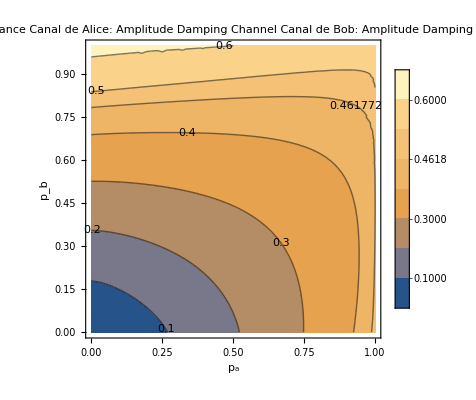

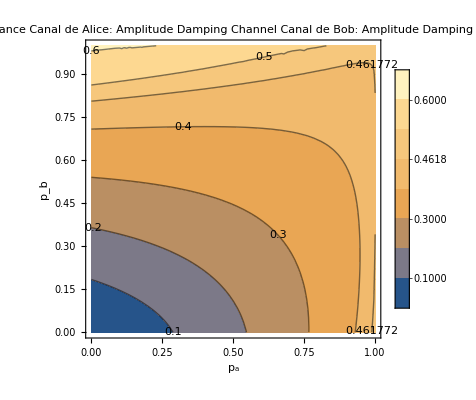

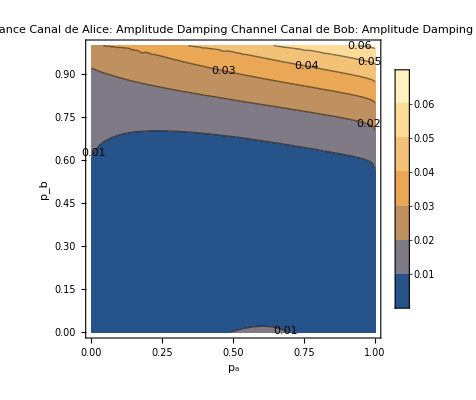

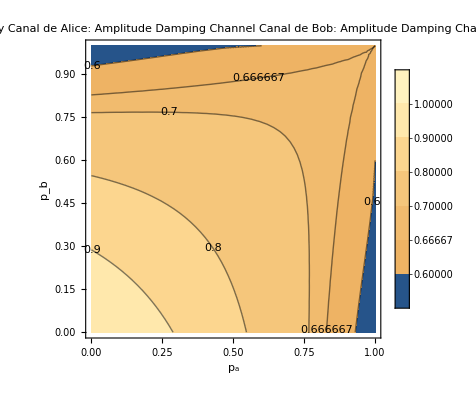

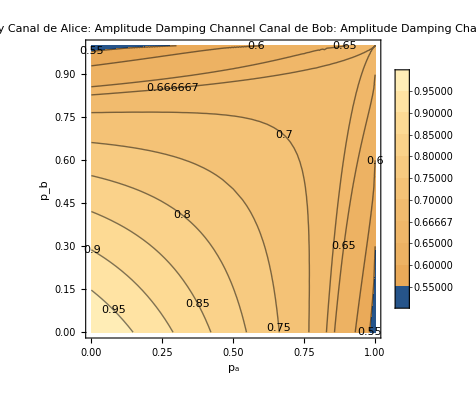

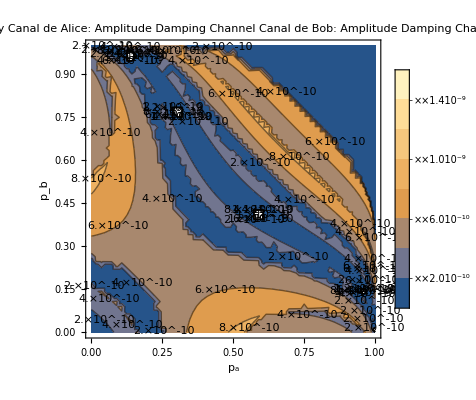

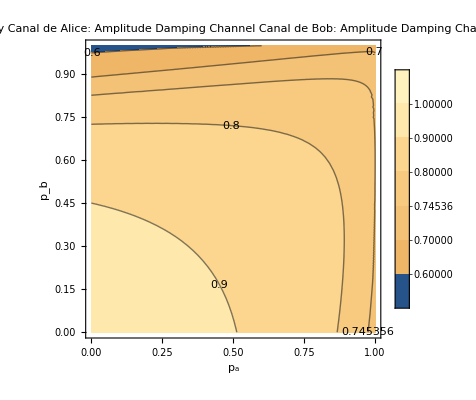

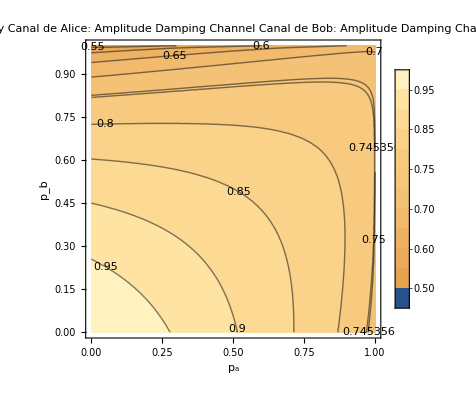

$Aborted

```mathematica
ForAllChannelsAndDistances[Function[{chA, chB, d, AvgDist, PaulisAvg}, 
(*ContourPlot*)
Print[ContourPlot[AvgDist[pA,pB],{pA,0,1},{pB,0,1},
FrameLabel->{Style[Subscript[p,a],Black,Italic,24],Style[Subscript[p,b],Black,Italic,24]},
Contours->(Sort[Append[FindDivisions[{#1,#2},#3], d[[3]]]]&),
ContourLabels->All,
PlotLegends->Automatic, 
PlotLabel-> d[[2]] <> "\nCanal de Alice: " <> GetChannelLabel[chA] <> "\nCanal de Bob: " <> GetChannelLabel[chB]
]];

Print[ContourPlot[PaulisAvg[pA,pB],{pA,0,1},{pB,0,1},
FrameLabel->{Style[Subscript[p,a],Black,Italic,24],Style[Subscript[p,b],Black,Italic,24]},
Contours->(Sort[Append[FindDivisions[{#1,#2},#3], d[[3]]]]&),
ContourLabels->All,
PlotLegends->Automatic, 
PlotLabel-> d[[2]] <> "\nCanal de Alice: " <> GetChannelLabel[chA] <> "\nCanal de Bob: " <> GetChannelLabel[chB]
]];
Print[ContourPlot[Abs[PaulisAvg[pA,pB] - AvgDist[pA,pB]],{pA,0,1},{pB,0,1},
FrameLabel->{Style[Subscript[p,a],Black,Italic,24],Style[Subscript[p,b],Black,Italic,24]},
Contours->(Sort[Append[FindDivisions[{#1,#2},#3], d[[3]]]]&),
ContourLabels->All,
PlotLegends->Automatic, 
PlotLabel-> d[[2]] <> "\nCanal de Alice: " <> GetChannelLabel[chA] <> "\nCanal de Bob: " <> GetChannelLabel[chB]
]];
]]
```